```mathematica
(* Fold along concentric circles by prescribing a starting ridge, the increment factor of the radii and the number of desired strips on the inner and outer side. TORUS with 4 strips and HYPAR with 3 strips are given as ready-to-run examples.*)

ClearAll["Global`*"];
Print[Now]

(* Definition of the starting ridge, computation of its length *)
(*
(* TORUS *)

a=4;p=5;q=1; 
startpar=0;endpar=2Pi;
torus[t1_,t2_]:={(a+Cos[t2])*Cos[t1],(a+Cos[t2])*Sin[t1],Sin[t2]};
gamma=torus[-q/p*t,t];
length=N[ArcLength[gamma,{t,startpar,endpar}]]*p; 
(* Increment factor of concentric circles and (#strips on the outer side, #strips on the inner side) *)
c=0.07; outerinner={2,2}; 
*)

(* HYPAR *)

k=3;r=1;
startpar=-Sqrt[(-1+Sqrt[1+k^2*r^2])/k^2] ;endpar=Sqrt[(-1+Sqrt[1+k^2*r^2])/k^2];
gamma=-{t,Sqrt[(r^2-t^2)/(1+k^2*t^2)],k*t*Sqrt[(r^2-t^2)/(1+k^2*t^2)]};
length=N[ArcLength[gamma,{t,startpar,endpar}]]*4;
(* Increment factor of concentric circles and (#strips on the outer side, #strips on the inner side) *)
c=0.095; outerinner={2,1}; 


(* Curvature and radius of a circle with the same length *)
curv=2Pi/length;
rad=1/curv;

(* Frenet Frame and speed of the chosen curve *)
fs=FrenetSerretSystem[gamma,t];
k=fs[[1,1]];tau=fs[[1,2]];

gammap=D[gamma,t];
vel=Sqrt[gammap.gammap];
```

Tue 9 Jun 2020 16:08:43GMT+2.

```mathematica
max=Max[outerinner];

(* Inizialization *)
kn=Table[t,{i,1,2},{j,1,max}]; (* Normal curvature *)
taur=Table[t,{i,1,2},{j,1,max}]; (* Relative torsion *)
sinalpha=Table[t,{i,1,2},{j,1,max}]; (* Sin of the angle between osc. and tg. plane *)
cosalpha=Table[t,{i,1,2},{j,1,max}]; (* Cos of ... *)
sinbeta=Table[t,{i,1,2},{j,1,max}]; (* Sin of the angle between ruling and tan of the ridge *)
cosbeta=Table[t,{i,1,2},{j,1,max}]; (* Cos of ...*)
betap=Table[t,{i,1,2},{j,1,max}]; (* First derivative in the arc-length of beta (wrt t) *)
reg=Table[t,{i,1,2},{j,1,max}]; (* Signed distance along the ruling of the regression curve *)
v=Table[t,{i,1,2},{j,1,max}]; (* Signed distance along the ruling of the next foldine *)
velocity=Table[vel,{i,1,2},{j,1,max}]; (* Velocity of the par of the ridge wrt t *)
radius=Table[rad,{i,1,2},{j,1,max}]; (* Radius of the foldline *)
geodcurvature=Table[curv,{i,1,2},{j,1,max}]; (* Curvature of the foldline *)

(* Initialize variables needed for the parametrization of the surfaces, comment if not needed *)
tan=Table[fs[[2,1]],{i,1,2},{j,1,max}]; (* Unit tg to the ridge *)
n=Table[{0,0,1},{i,1,2},{j,1,max}]; (* Darboux frame normal *)
u=Table[{0,1,0},{i,1,2},{j,1,max}]; (* Darboux frame tan X n*)
rul=Table[{t,0,0},{i,1,2},{j,1,max}];  (* Ruling *)
surf=Table[{0,0,0},{i,1,2},{j,1,max}]; (* Parametrization developable *)



(*Computation of the derivative of the angle function between osculating plane and tangent plane alpha*)
alphap[k_,r_,vel_]:=-(D[k,t]1/r)/((1/r)^2+k^2)/vel;
```

```mathematica
For[i=1,i≤2,i++,(*outer=1, inner=2*)

If[i==1,pom=+1,pom=-1]; (*plus if outer, minus if inner*)

For[j=1,j≤outerinner[[i]],j++,(*run over the foldlines on the chosen side*)


If[j==1, (*kn and taur of the first ridge*)

kn[[i,j]]=-pom*Sqrt[k^2-curv^2];
taur[[i,j]]=tau+alphap[kn[[i,j]],rad,velocity[[i,j]]];

];


If[j>1, (*kn and taur of subsequent ridges*)

radius[[i,j]]=rad(1+pom(j-1)c);
geodcurvature[[i,j]]=1/radius[[i,j]];

(* Sin and cos of the angle between correspondent tan of foldlines at start/end of a ruling and its first derivative in the arc-length *)
sindelta=1/radius[[i,j]]*v[[i,j-1]]*cosbeta[[i,j-1]];
cosdelta=radius[[i,j-1]]/radius[[i,j]]-1/radius[[i,j]]*v[[i,j-1]]*sinbeta[[i,j-1]];
deltap=D[sindelta,t]/velocity[[i,j-1]]/cosdelta;

(* Velocity wrt to the arc-length of the previous foldline and velocity wrt t *)
velnext=(deltap+geodcurvature[[i,j-1]])/geodcurvature[[i,j]];
velocity[[i,j]]=velnext*velocity[[i,j-1]];

(* Norm curv and rel tors of the next ridge wrt to the same dev surface *)
kntemp=(cosdelta*kn[[i,j-1]]+sindelta*taur[[i,j-1]])/velnext;
taurtemp=(-sindelta*kn[[i,j-1]]+cosdelta*taur[[i,j-1]])/velnext;

(* Norm curv and rel tors of the next ridge wrt to the next dev surface *)
kn[[i,j]]=-kntemp;
taur[[i,j]]=taurtemp-2alphap[kntemp,radius[[i,j]],velocity[[i,j]]];

];


(* Sin and Cos of the angle between osc. and tg. plane *)
sinalpha[[i,j]]=-kn[[i,j]]/Sqrt[kn[[i,j]]^2+geodcurvature[[i,j]]^2]; 
cosalpha[[i,j]]=geodcurvature[[i,j]]/Sqrt[kn[[i,j]]^2+geodcurvature[[i,j]]^2];

(* Sin and Cos of the angle between ruling and tan of the ridge and its first derivative in the arc-length  *)
sinbeta[[i,j]]=-kn[[i,j]]/Sqrt[(taur[[i,j]]^2+kn[[i,j]]^2)];
cosbeta[[i,j]]=taur[[i,j]]/Sqrt[(taur[[i,j]]^2+kn[[i,j]]^2)];
betap[[i,j]]=D[sinbeta[[i,j]],t]/velocity[[i,j]]/cosbeta[[i,j]];

(* Signed distance along the ruling of the regression curve *)
reg[[i,j]]=sinbeta[[i,j]]/(geodcurvature[[i,j]]+betap[[i,j]]);

(* Signed distance along the ruling of the next foldine *)
sign=Sign[sinbeta[[i,j]]/.t->startpar];
ctemp=rad(1+pom(j)c)/radius[[i,j]]-1;
v[[i,j]]=radius[[i,j]](sinbeta[[i,j]]-sign*Sqrt[sinbeta[[i,j]]^2+ctemp^2+2ctemp]);

(* Parametrization of the surface, comment if not needed *)

If[j==1,

(* Darboux frame *)
n[[i,j]]=cosalpha[[i,j]]*fs[[2,3]]-sinalpha[[i,j]]*fs[[2,2]];
u[[i,j]]=cosalpha[[i,j]]*fs[[2,2]]+sinalpha[[i,j]]*fs[[2,3]];

(* Ruling and parametrization *)
rul[[i,j]]=cosbeta[[i,j]]*tan[[i,j]]+sinbeta[[i,j]]*u[[i,j]];
surf[[i,j]]=gamma+s*v[[i,j]]*rul[[i,j]];

];


If[j>1,


(*Darboux frame of the next ridge wrt the same surface*)
tan[[i,j]]=cosdelta*tan[[i,j-1]]+sindelta*u[[i,j-1]];
unext=cosdelta*u[[i,j-1]]-sindelta*tan[[i,j-1]];
nnext=n[[i,j-1]];

(*Darboux frame of the next ridge wrt the next surface. Tangent does not change.*)
u[[i,j]]=(cosalpha[[i,j]]^2-sinalpha[[i,j]]^2)unext+(2cosalpha[[i,j]]*sinalpha[[i,j]])nnext;
n[[i,j]]=-(2cosalpha[[i,j]]*sinalpha[[i,j]])unext+(cosalpha[[i,j]]^2-sinalpha[[i,j]]^2)nnext;

(* Ruling and parametrization *)
rul[[i,j]]=(cosbeta[[i,j]]*tan[[i,j]]+sinbeta[[i,j]]*u[[i,j]]);
surfev=(surf[[i,j-1]])/.s->1;
surf[[i,j]]=surfev+s*v[[i,j]]*rul[[i,j]];

];

(* End of parametrization of the surface *)

];
];
```

Tue 9 Jun 2020 16:10:29GMT+2.

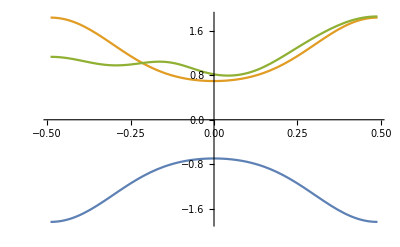

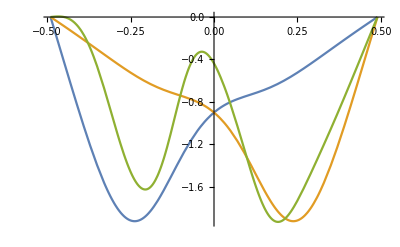

```mathematica
Print[Now]
Plot[{kn[[1,1]],kn[[2,1]],kn[[1,2]]},{t,startpar,endpar}]
Plot[{taur[[1,1]],taur[[2,1]],taur[[1,2]]},{t,startpar,endpar}] 

(* surf1=surf[[1,1]];
surf2=surf[[2,1]];
surf3=surf[[1,2]];
surf4=surf[[1,3]];
ParametricPlot3D[{surf1,surf2,surf3,surf4},{t,startpar,endpar},{s,0,1},Mesh->{10,5},PlotPoints->20, Boxed->False,Axes->False]
Print[Now] *)
```